# Modelo armamentístico de Richardson

## González Navarrete, Johan Jesús Hernandez Soc, Tomas David Hu Tang, Wei Le Monroy García, Zoé Abigail

Considera 2 naciones económicamente en competencia, Verde y Morado. Ambas naciones desean la paz y evitan la guerra, pero no son pacifistas. No buscarán la agresión pero no se detendrán ante nada para defenderse en caso de ataque. Ambas naciones creen en la autodefensa y lucharán para defender a su nación y su forma de vida.
Ambas naciones se encuentran en competición bajo un sensación de ”miedo mutuo”. Mientras más armas tenga una nación, la otra nación es motivada a comprar más armas. Pero no existe un presupuesto ilimitado, por lo que hay que asumir que un gasto excesivo en armamento reduce la razón de cambio en los gastos. La manera más sencilla de hacerlo es asumiento que el cambio en el armamento de cada nación es directa y negativamente proporcional a su propio gasto.
Aunado a esto podemos agregar un término que indique el sentir de cada país con respecto al otro. Dependiendo de si hay un sentir de amenaza o de buena voluntad del otro país hacia el suyo, aumenta o disminuye el gasto en armamento.
Las ecuaciones del modelo se muestran a continuación:

Donde  y  son los coeficientes de armamentaje, entre más grande el valor, más agresiva será la reacción de la nación al armamento de la otra. Los coeficientes  y  son las reacciones de la nación propia a su cantidad de armamento, lo cual desacelera el incremento del mismo. Finalmente los coeficientes  y  muestran el sentir de cada país hacia el otro, si estos son positivos, la nación ve a la otra como una amenaza; si son negativos, ven a la otra con buena voluntad para mantener la paz disminuye la carrera armamentista de la nación.

## (a) Para al menos 3 combinaciones de valores de los coeficientes realiza lo siguiente:

```mathematica
dx[x_,y_,a_,m_,r_]:=a y-m x+r;
dy[x_,y_,b_,n_,s_]:=b x-n y+s;
```

### i. Calcula los puntos de equilibrio del sistema.

```mathematica
equilibrio[a_,b_,m_,n_,r_,s_]:=FindRoot[{dx[x,y,a,m,r],dy[x,y,b,n,s]},{x,1},{y,1}];
```

### ii. Grafica los retratos fase de cada combinación mostrando los puntos estacionarios.

```mathematica
retrato[a_,b_,m_,n_,r_,s_,p_,min_,max_]:=StreamPlot[{dx[x,y,a,m,r],dy[x,y,b,n,s]},{x,min,max},{y,min,max},Axes->True,Epilog->{Red,PointSize[Large],Point[{p}]}];
```

### iii. Explica cuál es la situación modelada por ese caso particular de parámetros de acuerdo al comportamiento del retrato fase.

#### Observaciones generales

Notemos que, como nuestro sistema de ecuaciones diferenciales es lineal y la intersección
de dos lineas es un único punto a lo más, solo podemos tener un punto de equilibrio.
 pues representan el armamento de cada nación, y éstos al ser datos reales, no pueden ser negativos.
 no tendría sentido que el coeficiente de armamentaje fuese negativo, ya que se habla de un ámbito competitivo.
 porque a lo más que hace el sentir del pueblo sobre el armamento de su propia nación es desacelerarlo.
ℝ por lo ya definido en el planteamiento del problema, donde  representa indiferencia.
Finalmente, tiene sentido considerar números decimales para el nivel armamentista de cada país, pues éste puede ser medido con una estadística que no necesariamente es entera.

#### Caso 1:

```mathematica
equilibrio[1,1,4,3,5,5]
```

{x→1.81818,y→2.27273}

El punto de equilibrio es , lo cual tiene sentido pues , así que la nación  tiene una reacción menos negativa a su propio armamento, lo que les
permite desarrollar una mayor cantidad.

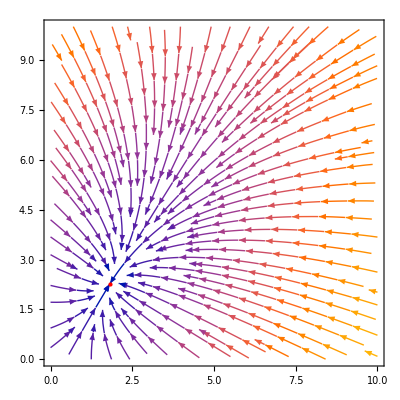

```mathematica
retrato[1,1,4,3,5,5,{1.8181818181818181,2.2727272727272725},0,10]
```

Vemos que es estable, lo que quiere decir que no importa la cantidad de armamento inicial de nuestras naciones, siempre llegaremos al punto de equilibrio en el que ambas están armadas y la nación  tiene una cantidad de armas ligeramente mayor.

La situación modelada es una en la que las reacciones de las naciones no son tan agresivas y son en magnitud iguales , y aunque ambas naciones se ven entre ellas como una amenaza , lo hacen en una pequeña magnitud, además tienen reacciones muy fuertes hacia su propio armamento, lo que causa que la carrera armamentística tenga un final definitivo.

#### Caso 2:

```mathematica
equilibrio[4,6,3,3,15,20]
```

{x→-8.33333,y→-10.}

Notamos que es imposible que una nación tenga armamento negativo, así que sabemos que el retrato fase no mostrará un equilibrio real factible.

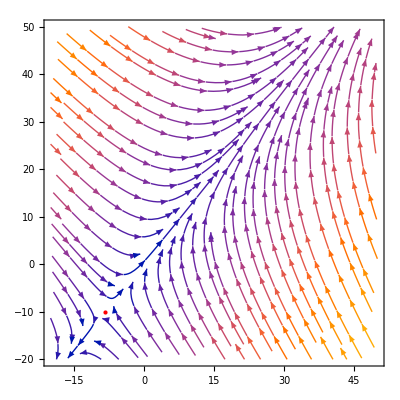

```mathematica
retrato[4,6,3,3,15,20,{-8.333333333333334,-10.},-20,50]
```

En donde vemos una carrera armamentística sin fin, es decir, cada nación acumula armamento de forma indefinida, lo cual es imposible por la limitación de recursos, así que en un ejemplo real creemos que esto llevaría a una confrontación directa.

Vemos que ambas naciones tienen reacciones bastante agresivas hacia el armamento de la nación enemiga , además, esta reacción es más fuerte que la reacción hacia su propio armamento , es decir, hay más aumento de armas para vencer al enemigo que decrecimiento de armas por cuenta propia. Además tenemos que ambas naciones se consideran amenaza mutuamente , por lo que interpretamos que tenemos confrontación directa inminente.

#### Caso 3:

```mathematica
equilibrio[1,5,2,2,-10,-20]
```

{x→40.,y→90.}

Donde vemos que es un punto “factible”, así que haremos el retrato fase para obtener más información.

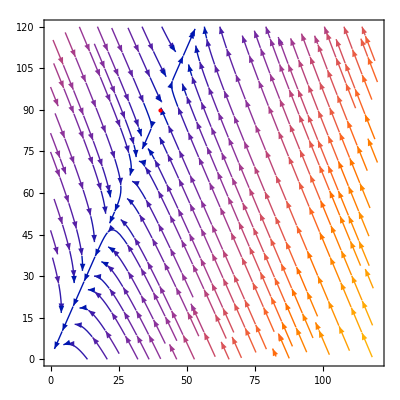

```mathematica
retrato[1,5,2,2,-10,-20,{40,90},0,120]
```

Este caso es mucho más interesante pues el resultado depende de la cantidad de armas iniciales, pues como tal, la solución de equilibrio es un punto silla. Vemos que si la relación del armamento de ambas naciones está por debajo de la variedad estable, tienen una cantidad de armas que ellos consideran pequeña, entonces el armamento empezará a disminuir hasta que ambas naciones estén desarmadas. Sin embargo, si hay una gran cantidad de armas (por encima de la variedad estable), ocurrirá algo similar al caso 2 (carrera armamentística sin fin, lo que podría llevar a confrontación). También hay un caso en el que ambas naciones tienden a tener un armamento fijo (sobre la variedad estable).

Vemos que la nación  tiene reacciones agresivas hacia el armamento de , esto se ve ya que , por otro lado  tiene una reacción menor , ambas naciones reaccionan de manera similar hacia su propio armamento , además se ven entre si con buena voluntad ya que  y ambos números son negativos. Ahora, notemos que cuando el armamento de ambas naciones es pequeño, como se ven con buena voluntad deciden decrecer su armamento y ambas terminan por estar desarmadas, sin embargo, si alguna de ellas tiene una cantidad de armas elevada, terminan por reaccionar de forma en que consiguen todavía más armas, lo cual nos lleva a una carrera armamentística sin fin incluso si no se ven de forma amenazante entre ellas.

## (b) Realiza un análisis de sensibilidad de los coeficientes , , y con respecto a una de las combinaciones de valores elegidas en el punto anterior.

Tomemos el Caso 1: , donde el punto de equilibrio es

Se sabe que dado cualquier coeficiente  , la sensibilidad respecto alguna variable , es:

```mathematica
(*Se obtienen las soluciones de (x,y) respecto a m*)
solm=Solve[{dx[x,y,1,m,5]==0,dy[x,y,1,3,5]==0},{x,y}]
```

{{x→20/(-1+3 m),y→(5 (1+m))/(-1+3 m)}}

```mathematica
(*Se calcula la sensibilidad de las variables respecto a m*)
smx=(D[solm[[1,1,2]],m]/.m->4)*4/1.818181
smy=(D[solm[[1,2,2]],m]/.m->4)*4/2.272727
```

-1.09091

-0.290909

Esto nos indica que la reducción del armamento en la nación  es de 1.09091% por cada aumento del 1% de , lo cual es una sensibilidad significativa, pues es casi la identidad por así decirlo. En cambio, como  sólo representa los sentimientos de la población  respecto a su propio armamento, lógicamente el de la nación  no se ve tan afectado en comparación, pues su reducción es del 0.290909% por cada 1% de . Realmente esto último sucede por cuestiones indirectas, como  reduce su armamento, entonces  no se encuentra en la necesidad de tener tanto.

```mathematica
(*Se obtienen las soluciones de (x,y) respecto a n*)
soln=Solve[{dx[x,y,1,4,5]==0,dy[x,y,1,n,5]==0},{x,y}]
```

{{x→(5 (1+n))/(-1+4 n),y→25/(-1+4 n)}}

```mathematica
(*Se calcula la sensibilidad de las variables respecto a n*)
snx=(D[soln[[1,1,2]],n]/.n->3)*3/1.818181
sny=(D[soln[[1,2,2]],n]/.n->3)*3/2.272727
```

-0.340909

-1.09091

Aquí se puede apreciar un comprotamiento completamente análogo al análisis de sensibilidad de , aunque  se ve más afectado por los sentimientos  de , que viceversa, pues por cada aumento del 1% de ,  reduce en 0.340909% su armamento, a diferencia del 0.290909% en el caso contrario. Se podría decir que  también son coeficientes de pacifismo, tal que el pueblo de  tiende más a buscar la paz (), y por eso su reducción de armas en respuesta del comportamiento de  es más significativo. Finalmente, la sensibilidad de  respecto a  es la misma que  respecto a , porque los otros dos parámetros son iguales ().

```mathematica
(*Se obtienen las soluciones de (x,y) respecto a r*)
solr=Solve[{dx[x,y,1,4,r]==0,dy[x,y,1,3,5]==0},{x,y}]
```

{{x→1/11 (5+3 r),y→(20+r)/11}}

```mathematica
(*Se calcula la sensibilidad de las variables respecto a r*)
srx=(D[solr[[1,1,2]],r]/.r->3)*3/1.818181
sry=(D[solr[[1,2,2]],r]/.r->3)*3/2.272727
```

0.45

0.12

En este caso, por cada cambio del 1% de  hay un cambio respectivo del 0.45% de ; esto tiene sentido, pues si se considera la otra nación más amenazante, se tiene que reforzar el armamento, pero no es tanto porque su sentido de pacifismo  no es tan diferente a su sentimiento de amenaza . Mientras que  también se refurza pero con sólo 0.12% por cada 1% de .

```mathematica
(*Se obtienen las soluciones de (x,y) respecto a s*)
sols=Solve[{dx[x,y,1,4,5]==0,dy[x,y,1,3,s]==0},{x,y}]
```

{{x→(15+s)/11,y→1/11 (5+4 s)}}

```mathematica
(*Se calcula la sensibilidad de las variables respecto a s*)
ssx=(D[sols[[1,1,2]],s]/.s->3)*3/1.818181
ssy=(D[sols[[1,2,2]],s]/.s->3)*3/2.272727
```

0.15

0.48

Se nota un comportamiento análogo pues , se consideran igual de amenazantes, aunque recordemos que  es ligeramente más pacífico que  (), y es por eso que se nota un pequeño aumento respecto al caso anterior. Por cada cambio del 1% de , se generan cambios del 0.15% y 0.48% en  y  respectivamente.